Ориентированный граф G задан списком ребер E с указанием веса ребра . Требуется, в соответствии с вариантом задания :
	1 Построить граф;
	2 Считая, что множество E есть множество ребер с пропускной способностью, равной весу
ребра, а G - сетевой граф с источником в вершине V1 и стоком в вершине V45, найти
максимальный поток в сети и указать хотя бы один минимальный разрез сети . 
	3 Отобразить распределение потока по ребрам графа .
Ход работы:
	1 Построить граф;

```mathematica
L={{1,4,7},{1,5,12},{1,6,7},{1,7,6},{1,10,6},{1,11,11},{1,12,10},{1,16,12},{4,18,7},{4,32,7},
{5,12,9},{5,19,8},{6,11,9},{6,24,5},{7,11,12},{7,19,9},{10,19,4},{10,20,4},{11,20,7},{11,21,8},
{11,24,7},{12,18,5},{12,21,12},{12,26,12},{16,19,10},{16,22,4},{18,22,12},{18,23,8},{18,32,12},
{19,20,8},{19,31,7},{19,32,6},{20,21,11},{20,26,11},{20,34,4},{20,40,5},{21,22,6},{21,31,5},
{22,26,4},{22,35,12},{23,32,6},{23,33,6},{24,28,8},{24,43,4},{26,28,4},{26,34,5},{26,38,11},
{28,34,6},{31,36,11},{31,38,6},{31,40,9},{32,40,9},{32,45,12},{33,35,12},{33,36,5},{34,38,4},
{34,42,5},{34,45,4},{35,38,7},{35,45,10},{36,45,7},{38,42,11},{38,43,8},{3,45,11},{40,45,6},
{42,45,10},{43,45,12}};
```

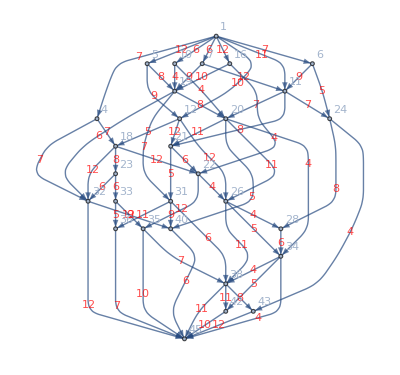

```mathematica
gr=Graph[{1->4,1->5,1->6,1->7,1->10,1->11,1->12,1->16,4->18,4->32,5->12,5->19,6->11,6->24,7->11,7->19,10->19,10->20,11->20,11->21,11->24,12->18,12->21,12->26,16->19,16->22,18->22,18->23,18->32,19->20,19->31,19->32,20->21,20->26,20->34,20->40,21->22,21->31,22->26,22->35,23->32,23->33,24->28,24->43,26->28,26->34,26->38,28->34,31->36,31->38,31->40,32->40,32->45,33->35,33->36,34->38,34->42,34->45,35->38,35->45,36->45,38->42,38->43,38->45,40->45,42->45,43->45},EdgeWeight->{7,12,7,6,6,11,10,12,7,7,9,8,9,5,12,9,4,4,7,8,7,5,12,12,10,4,12,8,12,8,7,6,11,11,4,5,6,5,4,12,6,6,8,4,4,5,11,6,11,6,9,9,12,12,5,4,5,4,7,10,7,11,8,11,6,10,12},EdgeLabels->"EdgeWeight",VertexLabels->"Name",EdgeLabelStyle->RGBColor[1, 0, 0]]
```

2 Считая, что множество E есть множество ребер с пропускной способностью, равной весу
ребра, а G - сетевой граф с источником в вершине V1 и стоком в вершине V45, найти
максимальный поток в сети и указать хотя бы один минимальный разрез сети .

```mathematica
weight={7,12,7,6,6,11,10,12,7,7,9,8,9,5,12,9,4,4,7,8,7,5,12,12,10,4,12,8,12,8,7,6,11,11,4,5,6,5,4,12,6,6,8,4,4,5,11,6,11,6,9,9,12,12,5,4,5,4,7,10,7,11,8,11,6,10,12};
```

```mathematica
FindMaximumFlow[gr,1,45,EdgeCapacity->weight]
```

71

```mathematica
minCut=FindMinimumCut[gr]
```

{0,{{45,42},{1,4,5,6,7,10,11,12,16,18,32,19,24,20,21,26,22,23,31,34,40,35,33,28,43,38,36}}}

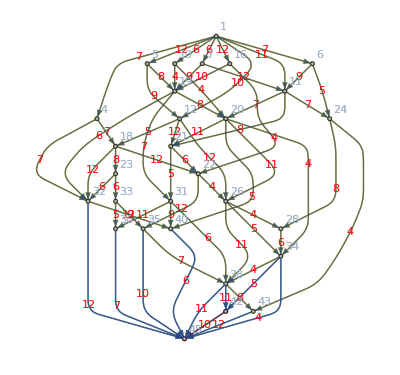

```mathematica
Show[HighlightGraph[gr,Map[Subgraph[gr,#]&,Last[minCut]]],SetProperty[gr,VertexLabels->"Name"],PlotRange->All]
```

3 Отобразить распределение потока по ребрам графа.

```mathematica
f=FindMaximumFlow[gr,1,45,"OptimumFlowData",EdgeCapacity->weight];
```

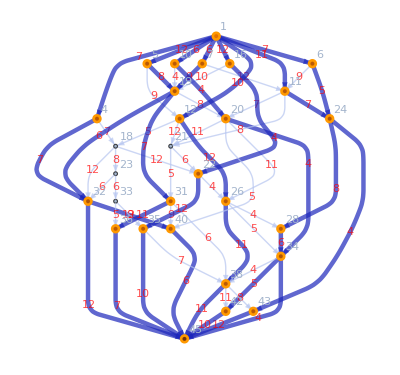

```mathematica
Annotation[f["FlowGraph"],{ EdgeLabels->{gr,f}}]
```

```mathematica
{1,4,5,6,7,10,11,12,16,18,32,19,24,20,21,26,22,23,31,34,40,35,33,28,43,38,36}
```

```mathematica
TableForm[Map[Normal,f["FlowMatrix"]],TableHeadings->{VertexList[gr],VertexList[gr]}]
```

| 1 | 4 | 5 | 6 | 7 | 10 | 11 | 12 | 16 | 18 | 32 | 19 | 24 | 20 | 21 | 26 | 22 | 23 | 31 | 34 | 40 | 35 | 33 | 28 | 43 | 38 | 36 | 45 | 42
1 | 0 | 7 | 12 | 7 | 6 | 6 | 11 | 10 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 6 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0
19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 4 | 0 | 0 | 0 | 0
20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 5 | 0 | 0 | 0 | 4 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
26 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 0
22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 0 | 0 | 0 | 0 | 0 | 0 | 0
23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
31 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 6 | 0 | 0
34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 4 | 5
40 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0
35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 10 | 0
33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
28 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
43 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 0
38 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 11 | 4
36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0
45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
42 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0